```mathematica
theta= UniformDistribution[{0,1}]
```

UniformDistribution[{0,1}]

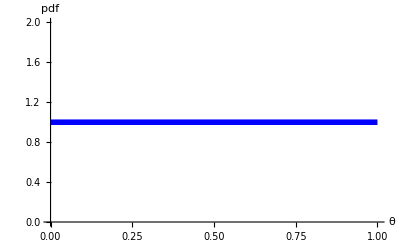

```mathematica
p1 = Plot[PDF[theta,x],{x,0,1},PlotStyle->{Blue,Thickness[0.01]},AxesLabel->{θ,pdf},BaseStyle->{FontSize->16}]
```

```mathematica
thetaSquared = TransformedDistribution[a^2,a\[Distributed]UniformDistribution[{0,1}]]
```

TransformedDistribution[x^2,x\[Distributed]UniformDistribution[{0,1}]]

```mathematica
PDF[TransformedDistribution[x^2,x\[Distributed]UniformDistribution[{0,1}]],x]
```

Piecewise[{{1/(2 √x), 0≤x≤1&&0≤√x≤1}, {0, True}}]

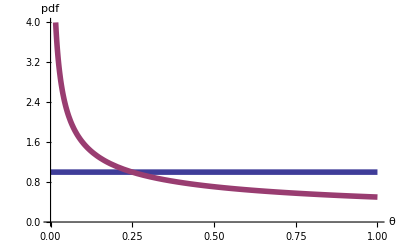

```mathematica
Plot[{PDF[theta,x],PDF[thetaSquared,x]},{x,0,1},PlotStyle->{Thickness[0.01]},AxesLabel->{θ,pdf},BaseStyle->{FontSize->16},PlotRange->{0,4}]
```

```mathematica
thetaCubed = TransformedDistribution[a^3,a\[Distributed]UniformDistribution[{0,1}]]
```

TransformedDistribution[x^3,x\[Distributed]UniformDistribution[{0,1}]]

```mathematica
PDF[TransformedDistribution[x^3,x\[Distributed]UniformDistribution[{0,1}]],x]
```

Piecewise[{{1/(3 x^(2/3)), 0≤x≤1&&0≤x^(1/3)≤1}, {0, True}}]

```mathematica
Plot[PDF[thetaCubed,x],{x,0,1}]
```

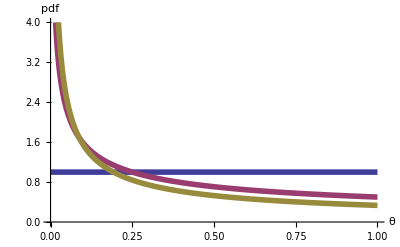

```mathematica
Plot[{PDF[theta,x],PDF[thetaSquared,x],PDF[thetaCubed,x]},{x,0,1},PlotStyle->{Thickness[0.01]},AxesLabel->{θ,pdf},BaseStyle->{FontSize->16},PlotRange->{0,4}]
```

```mathematica
thetaTen = TransformedDistribution[a^10,a\[Distributed]UniformDistribution[{0,1}]]
```

TransformedDistribution[x^10,x\[Distributed]UniformDistribution[{0,1}]]

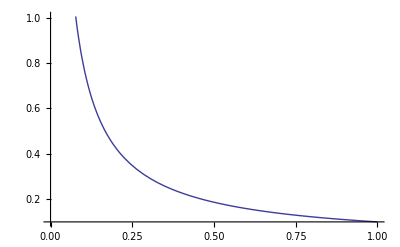

```mathematica
Plot[PDF[thetaTen,x],{x,0,1}]
```

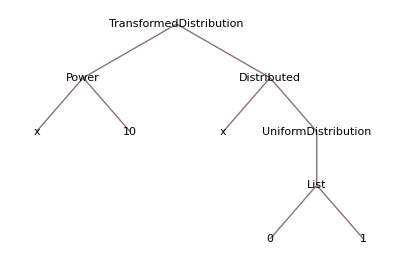

```mathematica
TreeForm[thetaTen]
```

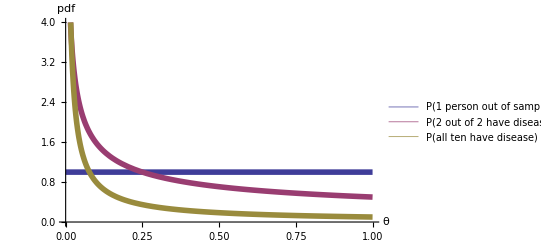

```mathematica
Plot[{PDF[theta,x],PDF[thetaSquared,x],PDF[thetaTen,x]},{x,0,1},PlotStyle->{Thickness[0.01]},AxesLabel->{θ,pdf},BaseStyle->{FontSize->16},PlotRange->{0,4},PlotLegends->Placed[{"P(1 person out of sample of 1 has disease)","P(2 out of 2 have disease)","P(all ten have disease)"},Below]]
```